## Chapter 7 Linear Algebra

### Section 7.1

We use the Which command to indicate the different types of entries we desire in the matrix.

```mathematica
Table[Which[i == j, i, i > j, 0, True, 1], {i, 10}, {j, 10}] // MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 4 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 5 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 6 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 7 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10)

The command DiagonalMatrix is used three times to create the entries on the various diagonals. The first input shows how to create the matrix displayed in the exercise. The second input generalizes the idea to create a matrix of any desired size. Note that it is also possible to use Table and RotateRight to accomplish the same thing; we show this alternative definition as well.

```mathematica
DiagonalMatrix[{2,3,4,5,6}]+DiagonalMatrix[{1,1,1,1},1]+DiagonalMatrix[{1},-4]//MatrixForm
```

(2 | 1 | 0 | 0 | 0
0 | 3 | 1 | 0 | 0
0 | 0 | 4 | 1 | 0
0 | 0 | 0 | 5 | 1
1 | 0 | 0 | 0 | 6)

```mathematica
wellMatrix[n_]:=DiagonalMatrix[Rest[Range[n+1]]]+DiagonalMatrix[Table[1,{n-1}],1]+DiagonalMatrix[{1},-(n-1)]
```

```mathematica
wellMatrix[6]//MatrixForm
```

(2 | 1 | 0 | 0 | 0 | 0
0 | 3 | 1 | 0 | 0 | 0
0 | 0 | 4 | 1 | 0 | 0
0 | 0 | 0 | 5 | 1 | 0
0 | 0 | 0 | 0 | 6 | 1
1 | 0 | 0 | 0 | 0 | 7)

```mathematica
wellMatrixAlternative[n_]:=Table[RotateRight[Join[{j+1,1},Table[0,{n-2}]],j-1],{j,n}]
```

```mathematica
wellMatrixAlternative[6]//MatrixForm
```

(2 | 1 | 0 | 0 | 0 | 0
0 | 3 | 1 | 0 | 0 | 0
0 | 0 | 4 | 1 | 0 | 0
0 | 0 | 0 | 5 | 1 | 0
0 | 0 | 0 | 0 | 6 | 1
1 | 0 | 0 | 0 | 0 | 7)

The command ReplacePart is used to create the blocks of integers. The input below also makes elegant use of the Map and Function commands. These are discussed in Section 8.4.

```mathematica
blockMatrix[n_]:=ArrayFlatten[ReplacePart[Table[0,{n}],Table[#,{#},{#}],#]&/@Range[n]]
```

```mathematica
blockMatrix[5]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4 | 4 | 4 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4 | 4 | 4 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4 | 4 | 4 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4 | 4 | 4 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 5 | 5 | 5 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 5 | 5 | 5 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 5 | 5 | 5 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 5 | 5 | 5 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 5 | 5 | 5 | 5)

### Section 7.2

First we append the identity matrix onto m1. It takes a single row operation to form the upper triangular matrix u from m1. The desired elementary matrix is the inverse of the matrix e which is the last two columns from m2 after the single row operation has been performed.

```mathematica
m1=({{1, 2}, {3, 4}})
```

{{1,2},{3,4}}

```mathematica
m2=ArrayFlatten[{{m1, IdentityMatrix[2]}}];
m2//MatrixForm
```

(1 | 2 | 1 | 0
3 | 4 | 0 | 1)

```mathematica
m2⟦2⟧=m2⟦2⟧-3m2⟦1⟧;
m2//MatrixForm
```

(1 | 2 | 1 | 0
0 | -2 | -3 | 1)

```mathematica
u=Take[m2,All,2];
u//MatrixForm
```

(1 | 2
0 | -2)

```mathematica
e=Take[m2,All,-2];
Inverse[e]//MatrixForm
```

(1 | 0
3 | 1)

```mathematica
Inverse[e].u//MatrixForm
```

(1 | 2
3 | 4)

```mathematica
Clear[m1,m2,u,e]
```

We produce the matrix using the wellMatrix command from exercise 2 in the previous section. We obtain the answer using RowReduce, and then carry out the row reduction process step by step, eventually reaching the same answer.

```mathematica
ℳ=ArrayFlatten[{{wellMatrix[5],Table[{721},{5}]}}];
ℳ//MatrixForm
```

(2 | 1 | 0 | 0 | 0 | 721
0 | 3 | 1 | 0 | 0 | 721
0 | 0 | 4 | 1 | 0 | 721
0 | 0 | 0 | 5 | 1 | 721
1 | 0 | 0 | 0 | 6 | 721)

```mathematica
RowReduce[ℳ]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 265
0 | 1 | 0 | 0 | 0 | 191
0 | 0 | 1 | 0 | 0 | 148
0 | 0 | 0 | 1 | 0 | 129
0 | 0 | 0 | 0 | 1 | 76)

```mathematica
ℳ⟦1⟧=1/2 ℳ⟦1⟧;
ℳ⟦5⟧=ℳ⟦5⟧-ℳ⟦1⟧;
ℳ//MatrixForm
```

(1 | 1/2 | 0 | 0 | 0 | 721/2
0 | 3 | 1 | 0 | 0 | 721
0 | 0 | 4 | 1 | 0 | 721
0 | 0 | 0 | 5 | 1 | 721
0 | -1/2 | 0 | 0 | 6 | 721/2)

```mathematica
ℳ⟦1⟧=ℳ⟦1⟧+ℳ⟦5⟧;
ℳ⟦2⟧=1/3 ℳ⟦2⟧;
ℳ⟦5⟧=ℳ⟦2⟧+2ℳ⟦5⟧;
ℳ//MatrixForm
```

(1 | 0 | 0 | 0 | 6 | 721
0 | 1 | 1/3 | 0 | 0 | 721/3
0 | 0 | 4 | 1 | 0 | 721
0 | 0 | 0 | 5 | 1 | 721
0 | 0 | 1/3 | 0 | 12 | 2884/3)

```mathematica
ℳ⟦2⟧=ℳ⟦2⟧-ℳ⟦5⟧;
ℳ⟦3⟧=1/4 ℳ⟦3⟧;
ℳ⟦5⟧=ℳ⟦3⟧-3ℳ⟦5⟧;
ℳ//MatrixForm
```

(1 | 0 | 0 | 0 | 6 | 721
0 | 1 | 0 | 0 | -12 | -721
0 | 0 | 1 | 1/4 | 0 | 721/4
0 | 0 | 0 | 5 | 1 | 721
0 | 0 | 0 | 1/4 | -36 | -10815/4)

```mathematica
ℳ⟦3⟧=ℳ⟦3⟧-ℳ⟦5⟧;
ℳ⟦4⟧=1/5 ℳ⟦4⟧;
ℳ⟦5⟧=ℳ⟦4⟧-4ℳ⟦5⟧;
ℳ//MatrixForm
```

(1 | 0 | 0 | 0 | 6 | 721
0 | 1 | 0 | 0 | -12 | -721
0 | 0 | 1 | 0 | 36 | 2884
0 | 0 | 0 | 1 | 1/5 | 721/5
0 | 0 | 0 | 0 | 721/5 | 54796/5)

```mathematica
ℳ⟦5⟧=5/721 ℳ⟦5⟧;
ℳ⟦4⟧=ℳ⟦4⟧-1/5 ℳ⟦5⟧;
ℳ⟦3⟧=ℳ⟦3⟧-36ℳ⟦5⟧;
ℳ⟦2⟧=ℳ⟦2⟧+12ℳ⟦5⟧;
ℳ⟦1⟧=ℳ⟦1⟧-6ℳ⟦5⟧;
ℳ//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 265
0 | 1 | 0 | 0 | 0 | 191
0 | 0 | 1 | 0 | 0 | 148
0 | 0 | 0 | 1 | 0 | 129
0 | 0 | 0 | 0 | 1 | 76)

### Section 7.3

We use the Dividers option to specify where we want vertical dividers and that we don’t want horizontal dividers.

```mathematica
Grid[{{1,2},{3,4}},Dividers->{{Black,{None},Black},None}]
```

1 | 2
3 | 4

This method of finding the inverse should be familiar to linear algebra students. After appending the identity matrix, Gaussian elimination is performed. Once the first square block has been reduce to the identity the matrix in the second square block will be the inverse.

```mathematica
mat1=({{1, 7, 5, 0}, {5, 8, 6, 9}, {2, 1, 6, 4}, {8, 1, 2, 4}});
```

```mathematica
mat2=ArrayFlatten[{{mat1, IdentityMatrix[4]}}];
mat2//MatrixForm
```

(1 | 7 | 5 | 0 | 1 | 0 | 0 | 0
5 | 8 | 6 | 9 | 0 | 1 | 0 | 0
2 | 1 | 6 | 4 | 0 | 0 | 1 | 0
8 | 1 | 2 | 4 | 0 | 0 | 0 | 1)

```mathematica
mat3=RowReduce[mat2];
mat3//MatrixForm
```

(1 | 0 | 0 | 0 | 46/993 | -56/993 | -73/1986 | 325/1986
0 | 1 | 0 | 0 | 86/993 | 68/993 | -133/993 | -20/993
0 | 0 | 1 | 0 | 23/331 | -28/331 | 129/662 | -3/662
0 | 0 | 0 | 1 | -148/993 | 137/993 | 19/1986 | -139/1986)

```mathematica
inv=Take[mat3,All,-4];
inv//MatrixForm
```

(46/993 | -56/993 | -73/1986 | 325/1986
86/993 | 68/993 | -133/993 | -20/993
23/331 | -28/331 | 129/662 | -3/662
-148/993 | 137/993 | 19/1986 | -139/1986)

```mathematica
inv.mat1//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Clear[mat1,mat2,mat3,inv]
```

### Section 7.4

Using the identity adj(A)=det(A) A^-1 we can find the adjoint. To check our result we need to enter the custom commands minorsMatrix and cofactorsMatrix. Don’t forget that the adjoint is the transpose of the matrix of cofactors.

```mathematica
mat=({{8, 0, 3, 7}, {9, 4, 2, 9}, {2, 8, 0, 7}, {8, 9, 7, 0}});
```

```mathematica
Det[mat]Inverse[mat]//MatrixForm
```

(434 | -581 | 313 | -20
203 | -126 | -41 | -51
-757 | 826 | -305 | -96
-356 | 310 | -227 | 64)

```mathematica
minorsMatrix[m_List?MatrixQ] := Map[Reverse, Minors[m], {0, 1}]
```

```mathematica
cofactorsMatrix[m_List?MatrixQ] :=Table[(-1)^(i+j),{i,Length[m]},{j,Length[m]}]*minorsMatrix[m]
```

```mathematica
Transpose[cofactorsMatrix[mat]]//MatrixForm
```

(434 | -581 | 313 | -20
203 | -126 | -41 | -51
-757 | 826 | -305 | -96
-356 | 310 | -227 | 64)

We need to first enter the custom commands minorsMatrix and cofactorsMatrix (from the previous exercise). We name our homemade determinant command det since Det is already taken. Testing on a random 5 by 5 matrix, we see it yields the same result as Det.

```mathematica
det[m_List?MatrixQ]:=Sum[m⟦1,i⟧*cofactorsMatrix[m]⟦1,i⟧,{i,1,Length[m]}]
```

```mathematica
With[{m=RandomInteger[10,{5,5}]},
{det[m],Det[m]}]
```

{-6375,-6375}

```mathematica
Clear[minorsMatrix,cofactorsMatrix,det,mat]
```

### Section 7.5

To create the pattern shown in the picture, the value of the entry in position (i,j) should be the absolute value of i-j. We use Table to create this list of values, and we then Flatten the list so it will be in the correct form for SparseArray.

```mathematica
s=SparseArray[Flatten[Table[{i,j}->Abs[i-j],{i,1,10},{j,1,10}]]]
```

SparseArray[…]

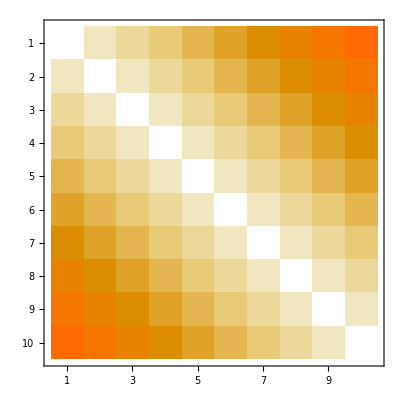

```mathematica
MatrixPlot[s]
```

```mathematica
Clear[s]
```

We can specify a Band that consists of smaller matrices.

```mathematica
s=SparseArray[Band[{1,1}]->Table[{{1,2},{3,4}},{i,1,6}]]
```

SparseArray[…]

```mathematica
MatrixForm[s]
```

(1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3 | 4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 4)

### Section 7.6

After performing Gaussian elimination on the augmented matrix we see that if a=±ⅈ there are no solutions, for the quantity 1+a^2=0 in this case, so the expressions in the rightmost column of the reduced matrix have a zero in their denominators and so do not evaluate to numbers. For any other value of a (in particular, for any real value of a), there is a unique solution given by the three expressions in the rightmost column of the reduced matrix.

```mathematica
Clear[mat,a];
mat=({{1, 2, -3, 4}, {2, -1, 5, 2}, {4, 3, a^2, a+3}});
```

```mathematica
RowReduce[mat]//MatrixForm
```

(1 | 0 | 0 | (57-7 a+8 a^2)/(5 (1+a^2))
0 | 1 | 0 | (-71+11 a+6 a^2)/(5 (1+a^2))
0 | 0 | 1 | (-7+a)/(1+a^2))

A standard form for the equation of a circle is a x^2+a y^2+b x+c y+d=0. Plugging the three points into this formula gives a homogeneous system of linear equations whose augmented matrix is used to find the solution graphed below.

```mathematica
mat=({{25, 4, -3, 1}, {41, -4, 5, 1}, {53, -2, 7, 1}});
```

```mathematica
NullSpace[mat]
```

{{-1,2,4,29}}

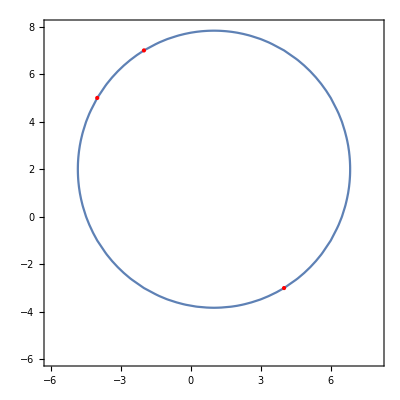

```mathematica
ContourPlot[-x^2+-y^2+2 x+4y+29==0,{x,-6,8},{y,-6,8},Epilog->{Red,Point[{{4,-3},{-4,5},{-2,7}}]}]
```

```mathematica
Clear[mat]
```

Writing the equations 2a+b=w and 3b+c=w, etc., we obtain the system shown below. We have already seen this matrix (Section 7.1, exercise 2) and we have row-reduced it (Section 7.2, exercise 2). Upon row reduction, there are an infinite number of solutions. Choosing w=721 will force all rope lengths to be integers, and since the numerators have no factors in common with 721, no smaller integer values are possible. We obtain: a=265, b=191, c=148, d=129, and e=76.

(2 | 1 | 0 | 0 | 0
0 | 3 | 1 | 0 | 0
0 | 0 | 4 | 1 | 0
0 | 0 | 0 | 5 | 1
1 | 0 | 0 | 0 | 6)·(a
b
c
d
e)=(w
w
w
w
w)

```mathematica
wellMatrix[n_]:=DiagonalMatrix[Rest[Range[n+1]]]+DiagonalMatrix[Table[1,{n-1}],1]+DiagonalMatrix[{1},-(n-1)]
```

```mathematica
ArrayFlatten[{{wellMatrix[5],Table[{w},{5}]}}]//MatrixForm
```

(2 | 1 | 0 | 0 | 0 | w
0 | 3 | 1 | 0 | 0 | w
0 | 0 | 4 | 1 | 0 | w
0 | 0 | 0 | 5 | 1 | w
1 | 0 | 0 | 0 | 6 | w)

```mathematica
ArrayFlatten[{{wellMatrix[5],Table[{w},{5}]}}]//RowReduce//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | (265 w)/721
0 | 1 | 0 | 0 | 0 | (191 w)/721
0 | 0 | 1 | 0 | 0 | (148 w)/721
0 | 0 | 0 | 1 | 0 | (129 w)/721
0 | 0 | 0 | 0 | 1 | (76 w)/721)

### Section 7.7

We form a matrix using the vectors as the rows and then use the Orthogonalize command.

```mathematica
Clear[m,o];
m=({{1, 2, 3}, {4, 5, 6}, {7, 7, 8}});
```

```mathematica
o=Orthogonalize[m];
o//MatrixForm
```

(1/(√14) | √(2/7) | 3/(√14)
4/(√21) | 1/(√21) | -2/(√21)
1/(√6) | -√(2/3) | 1/(√6))

```mathematica
Transpose[o].o//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Suppose o=(v_1 | v_2 | v_3
u_1 | u_2 | u_3
w_1 | w_2 | w_3) is an orthonormal matrix. Then o.o^t=(v_1 | v_2 | v_3
u_1 | u_2 | u_3
w_1 | w_2 | w_3)(v_1 | u_1 | w_1
v_2 | u_2 | w_2
v_3 | u_3 | w_3). Each entry along the diagonal in this product is the dot product of a row vector of o with itself, which will be 1 since these are unit vectors. Each non-diagonal entry is the dot product of a row vector with a different row vector, which will be 0 since the vectors are mutually orthogonal. While we used 3×3 matrices to illustrate the ideas, the argument holds for any n×n orthonormal matrix.

### Section 7.8

The LU-decomposition of a matrix is the decomposition of a matrix into the product of a lower triangular matrix and an upper triangular matrix. The built in command LUDecomposition does the hard work for us. We are able to recover the lower and upper triangular matrices from lu with the commands below:

```mathematica
m=({{2, -1, 0}, {-1, 2, 0}, {0, 0, 3}});
```

```mathematica
{lu,p,c}=LUDecomposition[m]
```

{{{-1,2,0},{-2,3,0},{0,0,3}},{2,1,3},0}

```mathematica
l=lu SparseArray[{i_,j_}/;j<i->1,{3,3}]+IdentityMatrix[3];
l//MatrixForm
```

(1 | 0 | 0
-2 | 1 | 0
0 | 0 | 1)

```mathematica
u=lu SparseArray[{i_,j_}/;j≥i->1,{3,3}];
u//MatrixForm
```

(-1 | 2 | 0
0 | 3 | 0
0 | 0 | 3)

```mathematica
l.u//MatrixForm
```

(-1 | 2 | 0
2 | -1 | 0
0 | 0 | 3)

This is equal to the original matrix if its rows are permuted according to the permutation p (the rows used for pivoting). In this case we have p={2,1,3}, so l.u is the matrix obtained from m by writing its rows in the order 2, 1, 3.

```mathematica
m⟦p⟧//MatrixForm
```

(-1 | 2 | 0
2 | -1 | 0
0 | 0 | 3)

```mathematica
Clear[o,m,l,u,lu,p,c]
```

### Section 7.9

We drew a bunny and made his reflection pink.

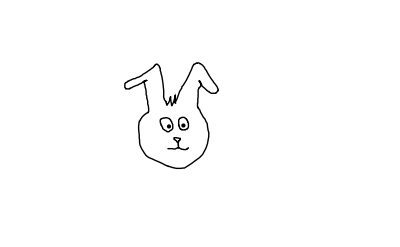
```mathematica
bunny=Cases[-Graphics-,Line[pts_]->pts,Infinity];
```

```mathematica
m=({{1, 0}, {0, -1}});
```

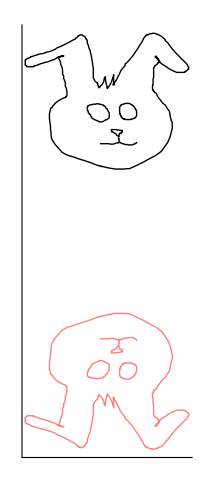

```mathematica
Graphics[{
Map[Line,bunny],
{Pink,Map[Line,Map[m.#&,bunny,{2}]]}
},Axes->True,Ticks->None]
```

```mathematica
Clear[bunny,m]
```

Here is the square gyrobicupola:

```mathematica
PolyhedronData["SquareGyrobicupola"]
```

-Graphics3D-

The first output below lists all available properties for this example. The vertices and faces outputs follow.

```mathematica
PolyhedronData["SquareGyrobicupola", "Properties"]
```

{AlternateNames,AlternateStandardNames,Amphichiral,Antiprism,Archimedean,ArchimedeanDual,BoundaryMeshRegion,Centroid,Chiral,Circumcenter,Circumradius,Circumsphere,Classes,Compound,Concave,Convex,DefaultOrientation,Deltahedron,DihedralAngles,Dipyramid,Dual,DualCompound,EdgeCount,EdgeLengths,Edges,Entity,Equilateral,FaceCount,Faces,GeneralizedDiameter,Graphics3D,GraphicsComplex,Image,ImplicitRegion,Incenter,InertiaTensor,Information,Inradius,Insphere,Isohedron,Johnson,KeplerPoinsot,MeshRegion,Midcenter,Midradius,Midsphere,MultipieceNetCoordinates,MultipieceNetFaceIndices,MultipieceNetImage,Name,Net,NetCount,NotationRules,Orientations,Platonic,PlatonicDual,Polyhedron,Prism,Pyramid,Quasiregular,Region,RegionFunction,Rhombohedron,Rigid,SchlaefliSymbol,SelfDual,Shaky,Skeleton,SpaceFilling,StandardName,StandardNames,Stellation,StellationCount,SurfaceArea,SymmetryGroup,SymmetryGroupString,Uniform,UniformDual,VertexCount,VertexSubsetHulls,Vertices,Volume,WythoffSymbol,Zonohedron}

```mathematica
vertices=N@PolyhedronData["SquareGyrobicupola", "VertexCoordinates"]
```

{{-0.5,-0.5,-0.707107},{-0.5,0.5,-0.707107},{0.,-0.707107,0.707107},{0.,0.707107,0.707107},{0.5,-0.5,-0.707107},{0.5,0.5,-0.707107},{-0.707107,0.,0.707107},{0.707107,0.,0.707107},{0.5,1.20711,0.},{-0.5,1.20711,0.},{-1.20711,0.5,0.},{-1.20711,-0.5,0.},{-0.5,-1.20711,0.},{0.5,-1.20711,0.},{1.20711,-0.5,0.},{1.20711,0.5,0.}}

```mathematica
faces=PolyhedronData["SquareGyrobicupola", "FaceIndices"]
```

{{4,7,3,8},{7,4,10,11},{3,7,12,13},{8,3,14,15},{4,8,16,9},{9,10,4},{11,12,7},{13,14,3},{15,16,8},{5,1,2,6},{10,9,6,2},{12,11,2,1},{14,13,1,5},{16,15,5,6},{6,9,16},{2,11,10},{1,13,12},{5,15,14}}

There are 16 vertices and 18 faces.

```mathematica
{Length[vertices],Length[faces]}
```

{16,18}

The input here is identical to that appearing in the text for the space shuttle example, except that the PlotRange is set to 2, and the EdgeForm[] directive has been eliminated so that the edges will render. We include the vertices and faces definitions using With so that the output is insulated from any changes made to these symbols later in the session. We use the displayMatrix command from the text to display the transformation matrix in the Manipulate.

```mathematica
displayMatrix[m_]:=MatrixForm@Map[NumberForm[Chop[N[#],10^-3],{3,2},NumberSigns->{"-"," "}]&,m,{2}]
```

```mathematica
With[{vertices=N@PolyhedronData["SquareGyrobicupola", "VertexCoordinates"],faces=PolyhedronData["SquareGyrobicupola", "FaceIndices"]},
Manipulate[
With[{m=RotationMatrix[θ,{1,0,0}].RotationMatrix[ϕ,{0,1,0}].RotationMatrix[φ,{0,0,1}]},
Labeled[
Graphics3D[GraphicsComplex[Table[m.v,{v,vertices}],Polygon[faces]],PlotRange->2],displayMatrix[m],{{Right,Top}}]],{θ,0,2π},{ϕ,0,2π},{φ,0,2π},SaveDefinitions->True]
]
```

```mathematica
Clear[vertices,faces,displayMatrix]
```